## Solution CP-11: Higher-dimensional systems

As usual, we first clear the memory of Mathematica:

```mathematica
Quit[]
```

## Higher-dimensional systems

For an overview of the relevant Mathematica commands, refer to chapter 12 of the tutorial, and also to chapters 9 & 10, since many commands are very similar to those used in linear systems (e.g., how to plot time and phase diagrams).

### Exercise 11-1: Chaos in a Three-Species Food Chain (Hastings & Powell, Ecology 72:896-903, 1991)

A three-species food chain: ⅆx/ⅆt=x·(1-x)-f_1(x)·y, ⅆy/ⅆt=f_1(x)·y-f_2(y)·z-d_1 y, and ⅆz/ⅆt=f_2(y)·z-d_2 z; with f_1(x)=a_1 x/(1+b_1 x) and f_2(y)=a_2 y/(1+b_2 y), fixed parameters a_1=5.0, a_2=0.1, b_2=2.0, d_1=0.4, d_2=0.01, and variable parameter b_1=2.0  to  6.2.

(a/b) Reproduce Figure 2 with Mathematica: Construct time plots and a 3D phase plot of the system with b_1=3.0.

```mathematica
timePhasePlot3S[b1_,x0_,y0_,z0_,tmin_,tmax_]:=Module[{params,f1,f2,eqX,eqY,eqZ,a1,a2,b2,d1,d2,sys,init,vars,sol},
params={a1->5.,a2->0.1,b2->2.,d1->0.4,d2->0.01};
f1[var_]:=a1*var/(1+b1*var);
f2[var_]:=a2*var/(1+b2*var);
eqX=D[x[t],t]==x[t]*(1-x[t])-f1[x[t]]*y[t];
eqY=D[y[t],t]==f1[x[t]]*y[t]-f2[y[t]]*z[t]-d1*y[t];
eqZ=D[z[t],t]==f2[y[t]]*z[t]-d2*z[t];
sys={eqX,eqY,eqZ};
init={x[0]==x0,y[0]==y0,z[0]==z0};
vars={x[t],y[t],z[t]};
sol=Flatten[NDSolveValue[{sys/.params,init},{vars},{t,0,tmax}]];
plX=Plot[sol[[1]],{t,tmin,tmax},PlotStyle->Blue,PlotRange->{{tmin,tmax},{0,1}}];
plY=Plot[sol[[2]],{t,tmin,tmax},PlotStyle->Red,PlotRange->{{tmin,tmax},{0,1}}];
plZ=Plot[sol[[3]],{t,tmin,tmax},PlotStyle->Green,PlotRange->{{tmin,tmax},{0,15}}];
(*plXYZ=Plot[sol,{t,tmin,tmax},PlotStyle->{Blue,Red,Green}];*)
pl3D=ParametricPlot3D[sol,{t,tmin,tmax},BoxRatios->1, AxesLabel->{"X","Y","Z"}];
GraphicsGrid[{{plX,plY},{plZ,pl3D}},ImageSize->Large]
]
```

```mathematica
Manipulate[timePhasePlot3S[b1,x0,y0,z0,tmin,tmax],{b1,3},{{x0,0.75},0,1},{{y0,0.175},0,.5},{{z0,7},5,10},{tmin,5000},{tmax,6500}]
```

(c) Study what happens to your plots of (b) when you vary b1 in the same way as indicated in Table 1.

```mathematica
Manipulate[timePhasePlot3S[b1,x0,y0,z0,tmin,tmax],{{b1,3},2,6.2,0.1,Appearance->"Labeled"},{{x0,0.75},0,1,Appearance->"Labeled"},{{y0,0.175},0,.5,Appearance->"Labeled"},{{z0,7},5,10,Appearance->"Labeled"},{tmin,5000},{tmax,6500}]
```

Note that for b1 = 2, the lower end of the b1 range, we have a stable equilibrium (even though the plot for z shows oscillations, look at the scale!), but slightly adjusting b1 to a value larger than 2 will give the limit cycles. 

(d) Reproduce Figure 3.

```mathematica
trajectoryPlot3S[b1_,x0_,y0_,z0_,tmin_,tmax_,epsx_,epsy_,epsz_]:=Module[{params,f1,f2,eqX,eqY,eqZ,a1,a2,b2,d1,d2,sys,init1,init2,vars,sol1,sol2},
params={a1->5.,a2->0.1,b2->2.,d1->0.4,d2->0.01};
f1[var_]:=a1*var/(1+b1*var);
f2[var_]:=a2*var/(1+b2*var);
eqX=D[x[t],t]==x[t]*(1-x[t])-f1[x[t]]*y[t];
eqY=D[y[t],t]==f1[x[t]]*y[t]-f2[y[t]]*z[t]-d1*y[t];
eqZ=D[z[t],t]==f2[y[t]]*z[t]-d2*z[t];
sys={eqX,eqY,eqZ};
init1={x[0]==x0,y[0]==y0,z[0]==z0};
init2 ={x[0]==x0+epsx,y[0]==y0+epsy,z[0]==z0+epsz};
vars={x[t],y[t],z[t]};
sol1=Flatten[NDSolveValue[{sys/.params,init1},{vars},{t,0,tmax}]];
sol2=Flatten[NDSolveValue[{sys/.params,init2},{vars},{t,0,tmax}]];
pl1=Plot[sol1[[1]]-sol2[[1]],{t,tmin,tmax},PlotRange->All,PlotStyle->Magenta];
pl2=Plot[{sol1[[1]],sol2[[1]]},{t,tmin,tmax},PlotRange->All,PlotStyle->{Blue,Red}];
GraphicsColumn[{pl1,pl2},ImageSize->Medium]
]
```

```mathematica
Manipulate[trajectoryPlot3S[b1,x0,y0,z0,tmin,tmax,epsx,epsy,epsz],{b1,3},{{x0,0.75},0,1,Appearance->"Labeled"},{{y0,0.175},0,.5,Appearance->"Labeled"},{{z0,7},5,10,Appearance->"Labeled"},{tmin,5000},{tmax,6000},{epsx,0.01},{epsy,0},{epsz,0}]
```

(e) Try to reproduce Figure 4. F(z,b_1)=?

```mathematica
Quit[]
```

```mathematica
zz[b1_,x0_,y0_,z0_,tmin_,tmax_]:=Module[{params,f1,f2,eqX,eqY,eqZ,a1,a2,b2,d1,d2,sys,init,vars,sol},
params={a1->5.,a2->0.1,b2->2.,d1->0.4,d2->0.01};
f1[var_]:=a1*var/(1+b1*var);
f2[var_]:=a2*var/(1+b2*var);
eqX=D[x[t],t]==x[t]*(1-x[t])-f1[x[t]]*y[t];
eqY=D[y[t],t]==f1[x[t]]*y[t]-f2[y[t]]*z[t]-d1*y[t];
eqZ=D[z[t],t]==f2[y[t]]*z[t]-d2*z[t];
sys={eqX,eqY,eqZ};
init={x[0]==x0,y[0]==y0,z[0]==z0};
vars={x[t],y[t],z[t]};
sol=Flatten[NDSolveValue[{sys/.params,init},{vars},{t,0,tmax}]];
sol[[3]]
];
(*Do[Print[N[Evaluate[zz[3,0.75,0.175,7,1,100]/.t->t0]]],{t0,0,12}]*)
Findmaxima[b1_,x0_,y0_,z0_,tmin_,tmax_,eps_]:=Module[{tt,zt,zmax,ztriplet},
zzz=zz[b1,x0,y0,z0,tmin,tmax];
zmax={};
tt=tmin+eps;
ztriplet={N[zzz/.t->tt-eps],N[zzz/.t->tt],N[zzz/.t->tt+eps]};
If[Max[ztriplet]==ztriplet[[2]],zmax=Append[zmax,{b1,ztriplet[[2]]}]];
While[tt<tmax-2*eps,
tt=tt+eps;
ztriplet={ztriplet[[2]],ztriplet[[3]],zzz/.t->tt+ eps};
If[Max[ztriplet]==ztriplet[[2]],zmax=Append[zmax,{b1,ztriplet[[2]]}]];
];
zmax
];
```

```mathematica
Findmaxima[3.0, 0.75, 0.175, 7, 5000, 6000, 0.05]
```

{{3.,8.32186},{3.,8.92138},{3.,10.2101},{3.,8.6611},{3.,10.4387},{3.,8.06847},{3.,8.57961},{3.,10.3685},{3.,8.22327},{3.,8.78593},{3.,10.4192},{3.,8.10993},{3.,8.63425},{3.,10.4211},{3.,8.10565},{3.,8.62859},{3.,10.4165},{3.,8.11551},{3.,8.64164},{3.,10.4267},{3.,8.09361}}

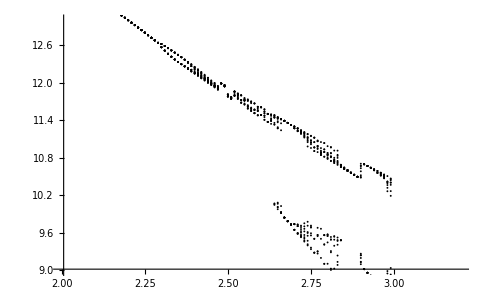

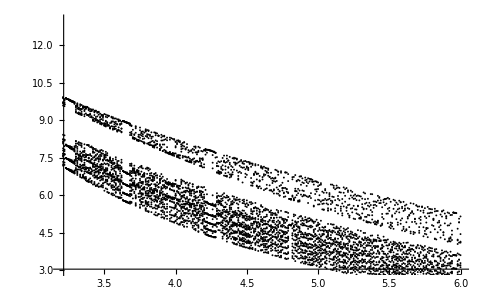

```mathematica
eps1 = 0.05;
eps2=0.01;
pts = Findmaxima[2.0001,0.75,0.175,7,5000,6000,eps1];
Do[pts = Append[pts,Findmaxima[b1,0.75,0.175,7,15000,16000,eps1]],{b1,2.0001+eps2,3.2,eps2}];
ListPlot[pts,PlotRange->{{2,3.2},{9,13}},PlotStyle->Black]
eps2=0.01;
pts = Findmaxima[3.2,0.75,0.175,7,5000,6000,eps1];
Do[pts = Append[pts,Findmaxima[b1,0.75,0.175,7,15000,16000,eps1]],{b1,3.2+eps2,6,eps2}];
ListPlot[pts,PlotRange->{{3.2,6},{3,13}},PlotStyle->Black]
```

### Exercise 11-2: Omnivory Creates Chaos in Simple Food Web Models (Tanabe & Namba (Ecology 86:3411-3414, 2005)

A simple food web model: (ⅆ N_1)/ⅆt=N_1·(b_1-a_11 N_1-a_12 N_2-a_13 N_3), (ⅆ N_2)/ⅆt=N_2·(-b_2+a_21 N_1-a_23 N_3), and (ⅆ N_3)/ⅆt=N_3·(-b_3+a_31 N_1+a_32 N_2).

(a) Try to reproduce Figure 1 with parameters b_1=5, b_2=1, b_3=1.2, a_11=0.4, a_12=a_21=a_23=a_32=1.

First, we want to find the equilibria as a function of a13 and a31. Then we determine their stability by looking at the eigenvalues.

```mathematica
eq1=N1*(b1-a11*N1-a12*N2-a13*N3);
eq2=N2*(-b2+a21*N1-a23*N3);
eq3=N3*(-b3+a31*N1+a32*N2);
param={b1->5,b2->1,b3->1.2,a11->0.4,a12->1,a21->1,a23->1,a32->1};
sol=Values[NSolve[{eq1==0,eq2==0,eq3==0},{N1,N2,N3}]/.param]
```

{{0.,1.2,-1.},{(1. (-3.8-1. a13))/(-0.4-1. a13+1. a31),(1. (0.48+1.2 a13-5. a31-1. a13 a31))/(0.4+1. a13-1. a31),-(1. (3.4+1. a31))/(-0.4-1. a13+1. a31)},{1.2/a31,0.,-(1. (0.48-5. a31))/(a13 a31)},{12.5,0.,0.},{1.,4.6,0.},{0.,0.,0.}}

```mathematica
jac=D[{eq1,eq2,eq3},{{N1,N2,N3}}]/.param
MatrixForm[jac]
```

{{5-0.8 N1-N2-a13 N3,-N1,-a13 N1},{N2,-1+N1-N3,-N2},{a31 N3,N3,-1.2+a31 N1+N2}}

(5-0.8 N1-N2-a13 N3 | -N1 | -a13 N1
N2 | -1+N1-N3 | -N2
a31 N3 | N3 | -1.2+a31 N1+N2)

```mathematica
jac1=jac/.{N1->sol[[1,1]],N2->sol[[1,2]],N3->sol[[1,3]]};
jac2=jac/.{N1->sol[[2,1]],N2->sol[[2,2]],N3->sol[[2,3]]};
jac3=jac/.{N1->sol[[3,1]],N2->sol[[3,2]],N3->sol[[3,3]]};
jac4=jac/.{N1->sol[[4,1]],N2->sol[[4,2]],N3->sol[[4,3]]};
jac5=jac/.{N1->sol[[5,1]],N2->sol[[5,2]],N3->sol[[5,3]]};
jac6=jac/.{N1->sol[[6,1]],N2->sol[[6,2]],N3->sol[[6,3]]};
Eigenvalues[jac1]
Eigenvalues[jac2]
Eigenvalues[jac3]
Eigenvalues[jac4]
Eigenvalues[jac5]
Eigenvalues[jac6]
```

{-1.09545,1.09545,3.8+1. a13}

{1/(2.+5. a13-5. a31)Root[310.08+1632. a13+2346. a13^2+510. a13^3-3914. a31-11233. a13 a31-3730. a13^2 a31-275. a13^3 a31+6897. a31^2+295. a13 a31^2-875. a13^2 a31^2-125. a13^3 a31^2+2375. a31^3+1100. a13 a31^3+125. a13^2 a31^3+(86.4+228. a13+30. a13^2-888. a31+48. a13 a31+60. a13^2 a31-125. a31^2+70. a13 a31^2+25. a13^2 a31^2) #1+(7.6+2. a13) #1^2+#1^3&,1],1/(2.+5. a13-5. a31)Root[310.08+1632. a13+2346. a13^2+510. a13^3-3914. a31-11233. a13 a31-3730. a13^2 a31-275. a13^3 a31+6897. a31^2+295. a13 a31^2-875. a13^2 a31^2-125. a13^3 a31^2+2375. a31^3+1100. a13 a31^3+125. a13^2 a31^3+(86.4+228. a13+30. a13^2-888. a31+48. a13 a31+60. a13^2 a31-125. a31^2+70. a13 a31^2+25. a13^2 a31^2) #1+(7.6+2. a13) #1^2+#1^3&,2],1/(2.+5. a13-5. a31)Root[310.08+1632. a13+2346. a13^2+510. a13^3-3914. a31-11233. a13 a31-3730. a13^2 a31-275. a13^3 a31+6897. a31^2+295. a13 a31^2-875. a13^2 a31^2-125. a13^3 a31^2+2375. a31^3+1100. a13 a31^3+125. a13^2 a31^3+(86.4+228. a13+30. a13^2-888. a31+48. a13 a31+60. a13^2 a31-125. a31^2+70. a13 a31^2+25. a13^2 a31^2) #1+(7.6+2. a13) #1^2+#1^3&,3]}

{-(1. (-0.48-1.2 a13+5. a31+a13 a31))/(a13 a31),(0.5 (-0.48 a13^3 a31-4.89898 a13^3 √(0.0096 a31^2+0.096 a31^3-1. a31^4)))/(a13^3 a31^2),(0.5 (-0.48 a13^3 a31+4.89898 a13^3 √(0.0096 a31^2+0.096 a31^3-1. a31^4)))/(a13^3 a31^2)}

{11.5,-5.,-1.2+12.5 a31}

{-0.2+2.13542 ⅈ,-0.2-2.13542 ⅈ,3.4+1. a31}

{5.,-1.2,-1.}

The second equilibrium corresponds to the case where all species coexist. To plot the figure, we therefore find the points {a13,a31} for which the second equilibrium is positive for all three species and for which this equilibrium is stable which requires that the real part of all eigenvalues is negative. We do this by a call to Sow and Reap:

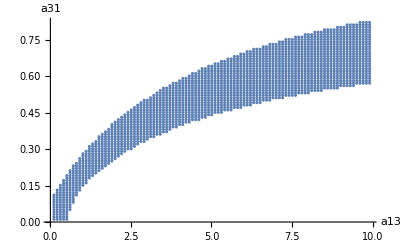

```mathematica
EV1[aa_,bb_]:=Eigenvalues[jac2]/.{a13->aa,a31->bb};
sol1[aa_,bb_]:=sol[[2,1]]/.{a13->aa,a31->bb};
sol2[aa_,bb_]:=sol[[2,2]]/.{a13->aa,a31->bb};
sol3[aa_,bb_]:=sol[[2,3]]/.{a13->aa,a31->bb};
(*sol1[10,1]
sol2[10,1]
sol3[10,1]
a1=10;
b1=1;
Re[EV1[a1,b1][[1]]]
Re[EV1[a1,b1][[2]]]
Re[EV1[a1,b1][[3]]]
(Re[EV1[1a1,b1][[1]]]<0 )&&(Re[EV1[a1,b1][[2]]]<0)&&(Re[EV1[a1,b1][[3]]]<0)&& (sol1[a1,b1]>0)&&(sol2[a1,b1]>0)&&(sol3[a1,b1]>0)
sol*)
pts=Reap[ (* collect the data generated by the Sow[] statements below *)
Do[Do[
If[(Re[EV1[aa,bb][[1]]]<0) &&(Re[EV1[aa,bb][[2]]]<0)&&(Re[EV1[aa,bb][[3]]]<0) && sol1[aa,bb]>0&&sol2[aa,bb]>0&&sol3[aa,bb]>0,Sow[{aa,bb}]],
{aa,0.11,10,0.1}],
{bb,0.011,1,0.01}]];
ListPlot[pts[[2]],AxesLabel->{a13,a31}]
```

```mathematica
Formally we should also check whether the third equilibrium (without the prey) is stable at the top. We do this by evaluating whether the real part of the eigenvalues in this equilibrium is negative. This is not shown here, because it is the same procedure as before for the second equilibrium.
```

(b) Reproduce their Fig. 2B (phase plot) and Fig. 2C (time plot) for a_13=10 and  a_31=0.1.  Vary the ‘bifurcation parameter’ a_13.

```mathematica
timePhasePlotFW[a13_,a31_,N01_,N02_,N03_,tmin_,tmax_]:=Module[{param,eq1,eq2,eq3,b1,b2,b3,a11,a12,a21,a23,a32,sys,init,vars,sol},
param={b1->5,b2->1,b3->1.2,a11->0.4,a12->1,a21->1,a23->1,a32->1};
eq1=D[N1[t],t]==N1[t]*(b1-a11*N1[t]-a12*N2[t]-a13*N3[t]);
eq2=D[N2[t],t]==N2[t]*(-b2+a21*N1[t]-a23*N2[t]);
eq3=D[N3[t],t]==N3[t]*(-b3+a31*N1[t]+a32*N2[t]);
sys={eq1,eq2,eq3};
init={N1[0]==N01,N2[0]==N02,N3[0]==N03};
vars={N1[t],N2[t],N3[t]};
sol=Flatten[NDSolveValue[{sys/.param,init},{vars},{t,0,tmax}]];
plot1=Plot[sol[[1]],{t,tmin,tmax},PlotStyle->Blue];
plot2=Plot[sol[[2]],{t,tmin,tmax},PlotStyle->Red];
plot3=Plot[sol[[3]],{t,tmin,tmax},PlotStyle->Green];
pl123=Plot[sol,{t,tmin,tmax},PlotStyle->{Blue,Red,Green}];
plot3D=ParametricPlot3D[sol,{t,tmin,tmax},BoxRatios->1, AxesLabel->{"N1","N2","N3"}];
GraphicsColumn[{plot3D,pl123},ImageSize->Large]
]
```

```mathematica
Manipulate[timePhasePlotFW[a13,a31,N01,N02,N03,tmin,tmax],{a13,10},{a31,0.1},{{N01,100},0,500},{{N02,10},0,50},{{N03,1},0,10},{tmin,0},{tmax,50},ContinuousAction->False]
```

NDSolveValue::ndsz: At t == 9.95671, step size is effectively zero; singularity or stiff system suspected.

```mathematica
Manipulate[timePhasePlotFW[a13,a31,N01,N02,N03,tmin,tmax],{a13,1,30},{a31,0.1},{{N01,100},0,500},{{N02,10},0,50},{{N03,1},0,10},{tmin,0},{tmax,50},ContinuousAction->False]
```

```mathematica
{2,3,4}
```

```mathematica
xx = {3,3};
xx = {xx,{4,4}}
xx={xx,{5,5}}
Flatten[xx]
xx[[5]]={3,3}
```

{{3,3},{4,4}}

{{{3,3},{4,4}},{5,5}}

{3,3,4,4,5,5}

Set::partw: Part 5 of {{{3,3},{4,4}},{5,5}} does not exist.

{3,3}